```mathematica
(*Put the ball dipped with ink on the center of rotating turntable and we can keep the trajectory of the ball until it rolls out of the turntable. Use a paper to keep track of the trajectory and measure the position of the points in polar coordinate. As the following figure shows:*)
```

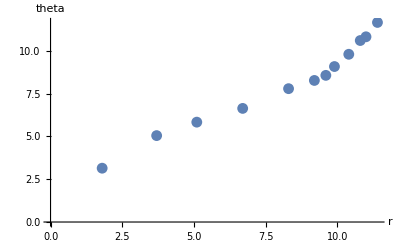

```mathematica
3.69/11.39
```

0.323968

```mathematica
(*As we can see, the points stands nearly to a line calculated with Least Sqaure Method*)
```

```mathematica
1.6123+0.79 x
```

```mathematica
(*1.6 can be explained by the fact that it is near to π/2. And the starting point is not shown by the ink so we lagged π/2 phase. We can reach to the conclusion that such trajectory is r=0.8*θ*)
```

```mathematica
listr={1.79,3.69,5.1,6.7,8.3,9.2,9.6,9.95,10.41,10.79,11,11.39};
listTheta={3.1,4.95,5.9,6.6,7.7,8.3,8.56,9.1,9.82,10.6,10.84,11.74}
```

{3.1,4.95,5.9,6.6,7.7,8.3,8.56,9.1,9.82,10.6,10.84,11.74}

```mathematica
Length/@{listr,listTheta}
```

{12,12}

```mathematica
listv={}
```

{}

```mathematica
For[i=2,i≤11,i++,AppendTo[listv,(listTheta[[i-1]]-listTheta[[i+1]])/(listr[[i-1]]-listr[[i+1]])]]
```

```mathematica
listr[[#]]&/@Range[2,11]
```

{3.69,5.1,6.7,8.3,9.2,9.6,9.95,10.41,10.79,11}

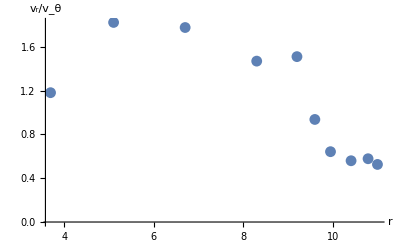

```mathematica
ListPlot[{%23,1/listv}//Transpose,AxesLabel->{r,Subscript[v, r]/Subscript[v, θ]}]
```

```mathematica
{3.1214501510574024,2.7956810631229225,3.768749999999998,5.644000000000006,6.086153846153853,10.239999999999984,15.477777777777765,18.58928571428572,18.65389830508474,20.89999999999996}
```

{3.12145,2.79568,3.76875,5.644,6.08615,10.24,15.4778,18.5893,18.6539,20.9}

```mathematica
ArcTan/@listv
```

{1.26076,1.22728,1.31143,1.39544,1.40794,1.47345,1.50628,1.51705,1.51724,1.52299}

```mathematica
1.227*180/3.14
```

70.3376